{0.433013,-0.433013}

If[t<0.4125,√((2 PE_0)/M_s0),√((2 PE_0)/M_s0)]

-Graphics3D-

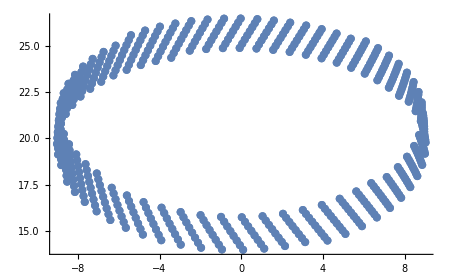

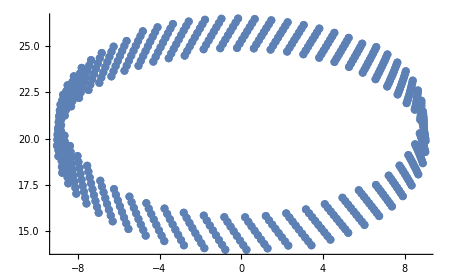

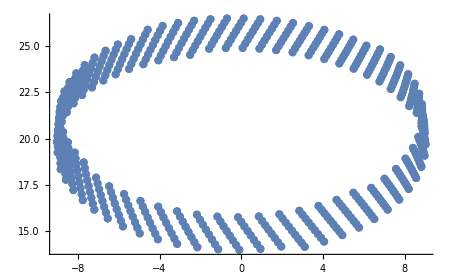

```mathematica
g= {0,0,-1.62}; (* Gravity vector *)
Subscript[X, i] = {0,0,2}; (* Initial position of bay origin (Vertex of exit plane and axis of rotation) (m) *)
Subscript[V, ibay]=6.4; (* Initial Bay Velocity (Obtained from spring force on total projectile mass) (m/s)*)
r = 0.04; (* Distance from stored lunasat COM to Bay AOR (m)*)
RPM = 300; (* Spin Rate (Revs per minute)*)
Subscript[V, li]=(RPM/60)r 2π; (* Linearized magnitude of lunasat relative velocity (m/s) *)
ϕ = π/6; (* Launch angle (Above horizion from y axis) (Rads) *)
dt = 0.0033; (* Change in time between ejections (s) *)
tf = dt * 125;
δ=0;

(* Rotational offset as a function of spinrate *)
(* Angle with angualar acceleration *)
(* θ[t_] := (RPM/60) t 2π-(1/2)(RPM/6000)t^2; *) 

(* Vonstant spinrate *)
 θ[t_] := δ+(RPM/60) (-t) 2π ;


Subscript[V, ri] = {{1,0,0},{0,-1,0},{-1,0,0},{0,1,0}}Subscript[V, li]; (* Relative velocity (Locked lunasats)*)
Subscript[X, ri] = {{0,1,0},{1,0,0},{0,-1,0},{-1,0,0}}r; (* Relative Positon (Locked lunasats)*)

Subscript[M, l]=0.005;
Subscript[M, s0]=0.005 * 125;
dx=25*(10^-2); (* compression length of lunasat bay spring *)
k=15; (* spring constant of lunasat bay (N/m) *)
γ=π/4;

(* TODO: Adjusted potential energy to account for 4 stacks ejected with energy of spring *)

Subscript[PE, 0]=((1/8)k dx^2 );
VV = √(2(Subscript[PE, 0]/Subscript[M, s0]));


Subscript[M, s][t_]:=Subscript[M, s0](1-t/tf);
PE[t_] := Subscript[PE, 0](1-t/tf);
KE[t_] := Subscript[PE, 0] - PE[t];


Subscript[a, bay]= √(2(Subscript[PE, 0]/(Subscript[M, s0]+2.5)))/tf;


Subscript[V, smag][t_]:= If[t<tf,√(2(Subscript[PE, 0]/Subscript[M, s0])),√(2(Subscript[PE, 0]/Subscript[M, s0]))];
Subscript[V, thrust][t_] := {Cos[γ],-Sin[γ]}Subscript[V, smag][t];
Print[Subscript[V, thrust][0]]
Print[Subscript[V, smag][t]]

Subscript[V, s][t_]:={{0,Subscript[V, thrust][t][[1]],Subscript[V, thrust][t][[2]]},{Subscript[V, thrust][t][[1]],0,Subscript[V, thrust][t][[2]]} ,{0,-Subscript[V, thrust][t][[1]],Subscript[V, thrust][t][[2]]},{-Subscript[V, thrust][t][[1]],0,Subscript[V, thrust][t][[2]]}};

(* Relative velocity rotated *)
Subscript[V, gi][t_]:={(Subscript[V, ri][[1]]+Subscript[V, s][t][[1]]).RotationMatrix[θ[t],{0,0,1}],(Subscript[V, ri][[2]]+Subscript[V, s][t][[2]]).RotationMatrix[θ[t],{0,0,1}],(Subscript[V, ri][[3]]+Subscript[V, s][t][[3]]).RotationMatrix[θ[t],{0,0,1}],(Subscript[V, ri][[4]]+Subscript[V, s][t][[4]]).RotationMatrix[θ[t],{0,0,1}]}

(* Relative position rotated *)
Subscript[X, gi][t_]:={Subscript[X, ri][[1]].RotationMatrix[θ[t],{0,0,1}],Subscript[X, ri][[2]].RotationMatrix[θ[t],{0,0,1}],Subscript[X, ri][[3]].RotationMatrix[θ[t],{0,0,1}],Subscript[X, ri][[4]].RotationMatrix[θ[t],{0,0,1}]}
(*
TEST = 0
Graphics3D[Table[Arrow[{Subscript[X, gi][TEST][[n]],Subscript[X, gi][TEST][[n]]+Subscript[V, gi][TEST][[n]]}],{n,1,4}]]
Graphics3D[Table[Arrow[{Subscript[X, gi][TEST+0.01][[n]].RotationMatrix[ϕ,{1,0,0}],(Subscript[X, gi][TEST+0.01][[n]]+Subscript[V, gi][TEST+0.01][[n]]).RotationMatrix[ϕ,{1,0,0}]}],{n,1,4}]]
*)
(* Trajectory as a function of initial position, initial velocity, gravity and time *)
Trajectory[ X_,V_,G_,T_]:=X+V T + (1/2)G T^2;

(* Trajectory of Bay as a function of time *)
Subscript[X, bay][t_] := Trajectory[Subscript[X, i],Subscript[V, ibay]*({0,0,1}.RotationMatrix[ϕ,{1,0,0}]),g + Subscript[a, bay]*({0,0,1}.RotationMatrix[ϕ,{1,0,0}]),t];

(* Trajectory of Baydoors (lunasat ejection points) as a function of time and column *)
Subscript[X, luna][t_,row_]:=(Subscript[X, gi][t][[row]]).RotationMatrix[ϕ,{1,0,0}] + Subscript[X, bay][t];

(* Trajectory of ejected lunasat as a function of ejection time, row and time after ejection *)
Ejected[T_,row_,t_]:=Trajectory[Subscript[X, luna][T,row],(Subscript[V, gi][T][[row]].RotationMatrix[ϕ,{1,0,0}])+Subscript[X, bay]'[T],g,t];

(* Final time / Time of impact as a function of eject time and row *)
Subscript[T, final][T_,row_]:=NSolve[Ejected[T,row,t][[3]]==0,t][[2]]

(* Impact as a function of lunasat row and col *)
Impact[i_,j_]  := {Ejected[i,j,t][[1]],Ejected[i,j,t][[2]]}/.Subscript[T, final][i,j]



(*Do[AppendTo[ejectList,Table[ParametricPlot3D[Ejected[i*dt,n,x],{x,0,t/.Subscript[T, final][i*dt,n]}],{n,1,4}]],{i,0,125}]*)
Show[
Table[ParametricPlot3D[Subscript[X, luna][t,n],{t,0,tf},PlotStyle->{Gray}],{n,1,4}],
Table[ParametricPlot3D[Ejected[0,n,x],{x,0,t/.Subscript[T, final][0,n]}],{n,1,4}],
(*Table[ParametricPlot3D[Ejected[dt,n,x],{x,0,t/.Subscript[T, final][dt,n]}],{n,1,4}],*)
PlotRange->All
]

Show[
Table[ListPlot[{Impact[n*dt,1]}],{n,1,125}],
Table[ListPlot[{Impact[n*dt,2]}],{n,1,125}],
Table[ListPlot[{Impact[n*dt,3]}],{n,1,125}],
Table[ListPlot[{Impact[n*dt,4]}],{n,1,125}],
PlotRange->All
]
δ=5π/180;
Show[
Table[ListPlot[{Impact[n*dt,1]}],{n,1,125}],
Table[ListPlot[{Impact[n*dt,2]}],{n,1,125}],
Table[ListPlot[{Impact[n*dt,3]}],{n,1,125}],
Table[ListPlot[{Impact[n*dt,4]}],{n,1,125}],
PlotRange->All
]
δ=7π/180;
Show[
Table[ListPlot[{Impact[n*dt,1]}],{n,1,125}],
Table[ListPlot[{Impact[n*dt,2]}],{n,1,125}],
Table[ListPlot[{Impact[n*dt,3]}],{n,1,125}],
Table[ListPlot[{Impact[n*dt,4]}],{n,1,125}],
PlotRange->All
]
(*
dt = 0.03
Show[
Table[ListPlot[{Impact[n*dt,1]}],{n,1,125}],
Table[ListPlot[{Impact[n*dt,2]}],{n,1,125}],
Table[ListPlot[{Impact[n*dt,3]}],{n,1,125}],
Table[ListPlot[{Impact[n*dt,4]}],{n,1,125}],
PlotRange->All
]

dt = 0.01;
Show[
Table[ListPlot[{Impact[n*dt,1]}],{n,1,125}],
Table[ListPlot[{Impact[n*dt,2]}],{n,1,125}],
Table[ListPlot[{Impact[n*dt,3]}],{n,1,125}],
Table[ListPlot[{Impact[n*dt,4]}],{n,1,125}],
PlotRange->All
]
dt = 0.001;
Show[
Table[ListPlot[{Impact[n*dt,1]}],{n,1,125}],
Table[ListPlot[{Impact[n*dt,2]}],{n,1,125}],
Table[ListPlot[{Impact[n*dt,3]}],{n,1,125}],
Table[ListPlot[{Impact[n*dt,4]}],{n,1,125}],
PlotRange->All
]
*)
```

```mathematica
Subscript[V, li]
```

```mathematica
Subscript[PE, 0]
```

15/32